# Lens geometry cell

## Setup

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory@NotebookDirectory[]
Get["MyPackage.wl"]
```

C:\Universita\MAGISTRALE\MasterThesis\Mathematica

```mathematica
NumDer[x_,y_]:=D[Interpolation[CombineVec[x,y]][h],h]/.h->x;
```

```mathematica
arrowcycle[]:= Line[x_]:>{Arrowheads[{0,0,0.05,0}],Arrow[x]}
```

```mathematica
opts={GridLines->Automatic,GridLinesStyle->LightGray,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->12},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

```mathematica
alldata=Import["lenscell_data.m"]
```

<|cellVal→{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,w0→1,tp0→1/40000,tf0→1/100000,ϵ1max→0.05},tankVal→{d→5,Pt→50000,Vtank→1,Vftot→1,f→0.1},gasVal→{patm→101325,Tstd→288.15,γair→1.4,ρstdair→1.225,cv→717.2,cp→1.0042}|>

```mathematica
celldata=alldata["cellVal"]
```

{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,w0→1,tp0→1/40000,tf0→1/100000,ϵ1max→0.05}

```mathematica
oneDOF=Import["1DOF.m"];
twoDOF=Import["2DOF.m"];
Row[{oneDOF//Dataset,Spacer@100,twoDOF//Dataset}]
```

## Model

```mathematica
data0nominal={l0->50 10^-3}//N;
data0nominal=Join[{h0->0.05 l0/.data0nominal},data0nominal]
```

{h0→0.0025,l0→0.05}

-Graphics-

```mathematica
solvegeom[h0_,l0_,pts_:100,interp_:0]:=Module[{θ0,R0,areaarc0,area,hvec,lcvec,Rtmp,Rvec,Δhvec,θvec,R,lc,α0,θ},
If[NumericQ[h0]&&NumericQ[l0],
θ0=α0/.FindRoot[((h0-l0/α0(1-Cos[α0/2])))==0,{α0,ArcCos[(2 h0)/l0]}];
R0=l0/θ0;
areaarc0=1/2 R0^2(θ0-Sin@θ0);
area=R lc(1-Cos[(l0-lc)/(2 R)])+R^2/2((l0-lc)/R-Sin[(l0-lc)/R]);
lcvec=LinSpace[0,l0-l0/3,pts];
Rtmp={R0};
Rvec=Flatten@Table[Rtmp=R/.FindRoot[(area==areaarc0)/.lc->lcvec[[i]],{R,Rtmp}],{i,1,Length@lcvec}];
θvec=(l0-lc)/R/.{lc->lcvec,R->Rvec};
hvec=R(1-Cos[θ/2])/.{R->Rvec,θ->θvec};
If[interp!=0,
Module[{lcint,Rint,θint},
lcint=Interpolation[Transpose[{hvec,lcvec}],InterpolationOrder->3];
Rint=Interpolation[Transpose[{hvec,Rvec}],InterpolationOrder->3];
θint=Interpolation[Transpose[{hvec,θvec}],InterpolationOrder->3];
{hvec,lcint,Rint,θint}]
,
{hvec,lcvec,Rvec,θvec}]
]]
```

```mathematica
Clear[DrawHalfCellDown,DrawHalfCellUp,DrawCell]
DrawHalfCellUp[hlcRθ_,hlcRθ0_List:{},xyshift_List:{0,0},tf0_:(tf0/.celldata)]:=
Module[{CarcAB,CarcCD,θAB,θCD,B,C,CarcAB0,CarcCD0,θAB0,θCD0,lc,R,h,θ,h0,lc0,R0,θ0,halfcell,xyshift0,halfcell0},
CarcAB={-lc/2,-(R-h)}+xyshift;θAB=π/2+{0,θ/2};B={-lc/2,h}+xyshift;
CarcCD={lc/2,-(R-h)}+xyshift;θCD=π/2+{0,-θ/2};C={lc/2,h}+xyshift;
halfcell={Circle[CarcAB,R,θAB],Line[{B,C}],Circle[CarcCD,R,θCD]};
If[Length@hlcRθ0==4,{h0,lc0,R0,θ0}=hlcRθ0;xyshift0={xyshift[[1]],xyshift[[2]]/(2hlcRθ[[1]]+tf0)(2hlcRθ0[[1]]+tf0)};
CarcAB0={-lc0/2,-(R0-h0)}+xyshift0;θAB0=π/2+{0,θ0/2};
CarcCD0={lc0/2,-(R0-h0)}+xyshift0;θCD0=π/2+{0,-θ0/2};
halfcell0={Circle[CarcAB0,R0,θAB0],Circle[CarcCD0,R0,θCD0]};
,halfcell0={}];
Graphics[{Darker@Red,Dashed,halfcell0,Thick,Dashing@None,halfcell/.{h->hlcRθ[[1]],lc->hlcRθ[[2]],R->hlcRθ[[3]],θ->hlcRθ[[4]]}}]
]
DrawHalfCellDown[hlcRθ_,hlcRθ0_List:{},xyshift_List:{0,0},tf0_:(tf0/.celldata)]:=
Module[{CarcAB,CarcCD,θAB,θCD,B,C,CarcAB0,CarcCD0,θAB0,θCD0,lc,R,h,θ,h0,lc0,R0,θ0,halfcell,xyshift0,halfcell0},
CarcAB={-lc/2,(R-h)}+xyshift;θAB=3π/2+{0,-θ/2};B={-lc/2,-h}+xyshift;
CarcCD={lc/2,(R-h)}+xyshift;θCD=3π/2+{0,θ/2};C={lc/2,-h}+xyshift;
halfcell={Circle[CarcAB,R,θAB],Line[{B,C}],Circle[CarcCD,R,θCD]};
If[Length@hlcRθ0==4,{h0,lc0,R0,θ0}=hlcRθ0;xyshift0={xyshift[[1]],xyshift[[2]]/(2hlcRθ[[1]]+tf0)(2hlcRθ0[[1]]+tf0)};
CarcAB0={-lc0/2,(R0-h0)}+xyshift0;θAB0=3π/2+{0,-θ0/2};
CarcCD0={lc0/2,(R0-h0)}+xyshift0;θCD0=3π/2+{0,θ0/2};
halfcell0={Circle[CarcAB0,R0,θAB0],Circle[CarcCD0,R0,θCD0]};
,halfcell0={}];
Graphics[{Darker@Red,Dashed,halfcell0,Thick,Dashing@None,halfcell/.{h->hlcRθ[[1]],lc->hlcRθ[[2]],R->hlcRθ[[3]],θ->hlcRθ[[4]]}}]
]
DrawCell[hlcRθ_,hlcRθ0_List:{},xyshift_List:{0,0},tf0_:(tf0/. celldata)]:=
Show[
DrawHalfCellUp[hlcRθ,hlcRθ0,xyshift,tf0],
DrawHalfCellDown[hlcRθ,hlcRθ0,xyshift,tf0]
]
```

### Test geometries

```mathematica
h0range=h0{0.5,1,1.5}/.data0nominal;l0range=l0{0.5,1,1.5}/.data0nominal;
h0strings=Table[StringJoin["h_0 = ",ScientString[h0range[[i]]//N,3]," [m]"],{i,1,Length@h0range}]
l0strings=Table[StringJoin["l_0 = ",ScientString[l0range[[i]]//N,3]," [m]"],{i,1,Length@l0range}]
```

{h_0 = 1.25×10^-3 [m],h_0 = 2.5×10^-3 [m],h_0 = 3.75×10^-3 [m]}

{l_0 = 2.5×10^-2 [m],l_0 = 5.×10^-2 [m],l_0 = 7.5×10^-2 [m]}

```mathematica
geomhl=Table[solvegeom[h0range[[i]],l0range[[j]],100],{i,1,Length@h0range},{j,1,Length@l0range}];(*geomhl[[i,j]] -> h0range[[i]],l0range[[j]]*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Manipulate[Column[
Table[Row[
Flatten@Table[{Block[{hlcRθ=geomhl[[i,j,;;,idx]],hlcRθ0=If[undef==1,geomhl[[i,j,;;,1]],{}],tf0=tf0/.celldata},
Show[DrawCell[hlcRθ,hlcRθ0],PlotLabel->Row[{h0strings[[i]],Spacer@10,l0strings[[j]]}],
Axes->True,ImageSize->350,PlotRange->{0.95l0range[[j]]{-1,1},1.2h0range[[i]]{-1,1}},AspectRatio->(5 h0range[[i]])/l0range[[3]],Frame->True,Evaluate@opts]],Spacer@10},{i,1,Length@h0range}]],{j,1,Length@l0range}]
],{idx,1,100,1},{{undef,1,"Undeformed"},{0,1}}]
```

## Cell analysis

### Double cell unit

```mathematica
cellidx=2;
```

```mathematica
nominalunit=solvegeom[h0/.data0nominal,l0/.data0nominal,1000,0];nominalunit[[1]]=4nominalunit[[1]];
hunom=nominalunit[[1]];lcnom=nominalunit[[2]];Rnom=nominalunit[[3]];θnom=nominalunit[[4]];
hnom=hunom/4;
```

```mathematica
Manipulate[Block[{hlcRθ=Flatten@{1/4 nominalunit[[1,idx]],nominalunit[[2;;4,idx]]},hlcRθ0=If[undef==1,Flatten@{1/4 nominalunit[[1,1]],nominalunit[[2;;4,1]]},{}],tf0=tf0/.celldata},
Show[
Table[DrawCell[hlcRθ,hlcRθ0,(i-1){0,2hlcRθ[[1]]+tf0},tf0],{i,1,2}],
PlotLabel->StringJoin["Δh = ",ScientString[4(hlcRθ0[[1]]-hlcRθ[[1]]),3], " [m]"],
Evaluate@opts,PlotRange->{0.6(l0/.data0nominal){-1,1},(h0/.data0nominal){-1.1,4}}
]]
,{idx,1,Length@nominalunit[[1]],1},{{undef,1,"Undeformed"},{0,1}}]
```

```mathematica
hunom=nominalunit[[1]];lcnom=nominalunit[[2]];Rnom=nominalunit[[3]];θnom=nominalunit[[4]];
```

```mathematica
Delta[x_]:=x[[1]]-x
```

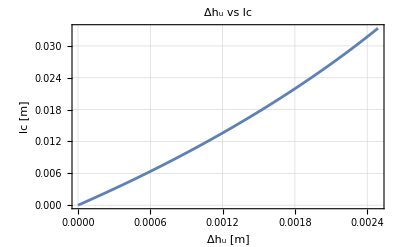
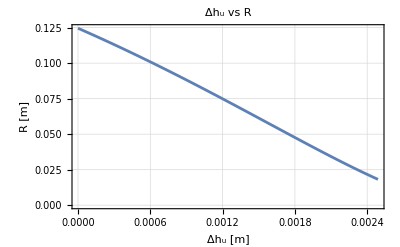
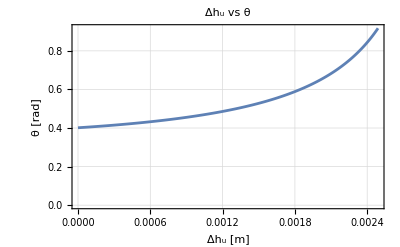

```mathematica
Row[{
ListPlot[CombineVec[Delta@hunom,lcnom],Joined->True,ImageSize->400,Evaluate@opts,PlotLabel->"Δh_u vs lc",FrameLabel->{"Δh_u [m]","lc [m]"}],Spacer@10,
ListPlot[CombineVec[Delta@hunom,Rnom],Joined->True,ImageSize->400,Evaluate@opts,PlotLabel->"Δh_u vs R",FrameLabel->{"Δh_u [m]","R [m]"}],Spacer@10,
ListPlot[CombineVec[Delta@hunom,θnom],Joined->True,ImageSize->400,Evaluate@opts,PlotLabel->"Δh_u vs θ",FrameLabel->{"Δh_u [m]","θ [rad]"}]
}]
```

#### Capacitance

```mathematica
CC=(((ϵp w0 lc[h])/(2 tp0))^-1+((ϵf w0 lc[h])/tf0)^-1)^-1//Simplify
```

(w0 ϵf ϵp lc[h])/(2 tp0 ϵf+tf0 ϵp)

```mathematica
Cnom=CC/.celldata/.lc[h]->lcnom;
```

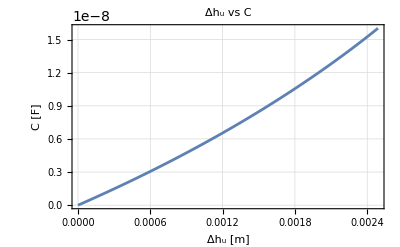

```mathematica
ListPlot[CombineVec[Delta@hunom,Cnom],Joined->True,Evaluate@opts,FrameLabel->{"Δh_u [m]","C [F]"},PlotLabel->"Δh_u vs C"]
```

#### Force

```mathematica
Vrange=Range[0,6000,2000];
Vstrings=Table[StringJoin["V = ",ScientString[Vrange[[i]],3]," [V]"],{i,1,Length@Vrange}];
```

```mathematica
F[hh_,V_]:=(-V^2/8 D[CC,h])(*dhu = 4dh*)
```

```mathematica
Fnom[VV_]:=F[h,V]/.lc'[h]->NumDer[hnom,lcnom]/.celldata/.V->VV
```

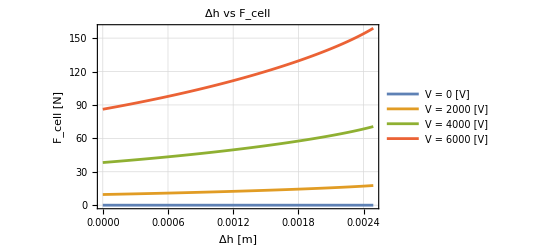

```mathematica
ListPlot[Table[CombineVec[Delta@hunom,Fnom[Vrange[[i]]]],{i,1,Length@Vrange}],Joined->True,Evaluate@opts,FrameLabel->{"Δh [m]","F_cell [N]"},PlotLabel->"Δh vs F_cell",PlotLegends->AddLegend[Vstrings],PlotRange->All]
```

```mathematica
Area0=1/2 R0^2(θ0-Sin@θ0);
```

```mathematica
Volf=2(2(w0(h(lc+2R Sin[θ/2])-Area0)))
```

4 w0 (h (lc+2 R Sin[θ/2])-1/2 R0^2 (θ0-Sin[θ0]))

```mathematica
Volfvec=Volf/.celldata/.{h->hnom,lc->lcnom,R->Rnom,θ->θnom,R0->Rnom[[1]],θ0->θnom[[1]]};
```

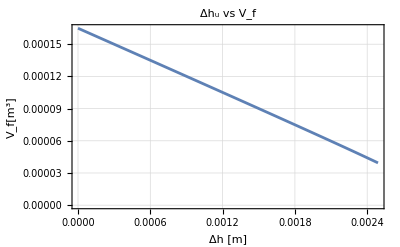

```mathematica
ListPlot[CombineVec[Delta@hunom,Volfvec],Joined->True,Evaluate@opts,FrameLabel->{"Δh [m]","V_f[m^3]"},PlotLabel->"Δh_u vs V_f"]
```

```mathematica
Uel=CumTrapz[Delta@hunom,Fnom[Last@Vrange]];
```

```mathematica
uel=Uel/Volfvec[[1]];
```

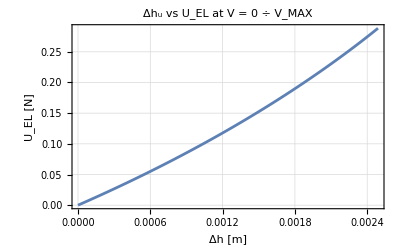
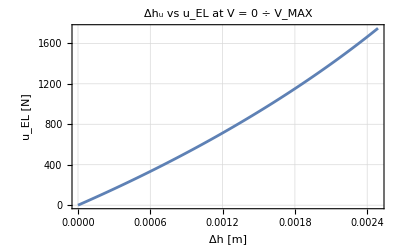

```mathematica
Row[{
ListPlot[CombineVec[Delta@hunom,Uel],Joined->True,Evaluate@opts,FrameLabel->{"Δh [m]","U_EL [N]"},PlotLabel->"Δh_u vs U_EL at V = 0 ÷ V_MAX"],
ListPlot[CombineVec[Delta@hunom,uel],Joined->True,Evaluate@opts,FrameLabel->{"Δh [m]","u_EL [N]"},PlotLabel->"Δh_u vs u_EL at V = 0 ÷ V_MAX"]
}]
```

### Varying h_0 and l_0

```mathematica
h0rangetest=h0{0.5,1,2}/.data0nominal;l0rangetest=l0{0.5,1,2}/.data0nominal;
geomhl1000=Table[solvegeom[h0rangetest[[i]],l0rangetest[[j]],1000],{i,1,Length@h0range},{j,1,Length@l0range}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
aspratios=Table[h0rangetest[[i]]/l0rangetest[[j]],{i,1,Length@h0range},{j,1,Length@l0range}]//N;aspratios//MatrixForm
```

(0.05 | 0.025 | 0.0125
0.1 | 0.05 | 0.025
0.2 | 0.1 | 0.05)

```mathematica
arsamel0=aspratios[[1;;3,2]]
```

{0.025,0.05,0.1}

```mathematica
smallerh0=geomhl1000[[1,2]];
nominalh0=geomhl1000[[2,2]];
biggerh0=geomhl1000[[3,2]];
```

```mathematica
geoms={smallerh0,nominalh0,biggerh0};
```

```mathematica
smallersamear=geomhl1000[[1,1]];
biggersamear=geomhl1000[[3,3]];
```

```mathematica
geomresc={smallersamear,nominalh0,biggersamear};
```

#### Animation

```mathematica
Manipulate[
Block[{tf0=tf0/.celldata},
Show[Table[DrawCell[geoms[[i,;;,idx]],If[undef==1,geoms[[i,;;,1]],{}]],{i,1,3}],PlotLabel->"h0/l0 = "<>ToString[arsamel0],
ImageSize->1000,Evaluate@opts,FrameLabel->{"x [m]","y [m]"}]]
,{idx,1,1000,1},{{undef,1,"Undeformed"},{0,1}}]
```

```mathematica
Manipulate[
Block[{tf0=tf0/.celldata},
Show[Table[DrawCell[geomresc[[i,;;,idx]],If[undef==1,geomresc[[i,;;,1]],{}]],{i,1,3}],ImageSize->1000,Evaluate@opts,FrameLabel->{"x [m]","y [m]"}]]
,{idx,1,1000,1},{{undef,1,"Undeformed"},{0,1}}]
```

### lc

#### Varying aspect ratio

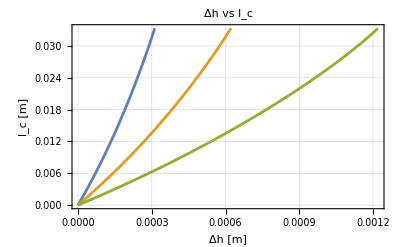
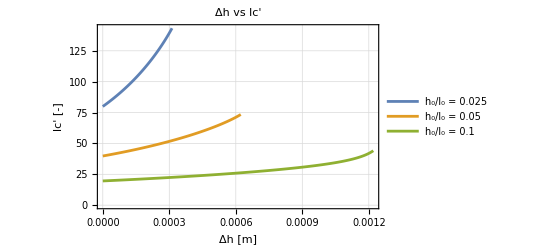

```mathematica
Row[{
ListPlot[Table[CombineVec[Delta@geoms[[i,1]],geoms[[i,2]]],{i,1,3}],Joined->True,Evaluate@opts,PlotRange->All,FrameLabel->{"Δh [m]","l_c [m]"},PlotLabel->"Δh vs l_c"],
ListPlot[Table[CombineVec[Delta@geoms[[i,1]],NumDer[Delta@geoms[[i,1]],geoms[[i,2]]]],{i,1,3}],Joined->True,Evaluate@opts,PlotRange->All,FrameLabel->{"Δh [m]","lc' [-]"},PlotLabel->"Δh vs lc'",PlotLegends->AddLegend[Table["h_0/l_0 = "<>ToString[arsamel0[[i]]],{i,1,Length@geoms}],Right,Bottom]]
}]
```

#### Rescaling

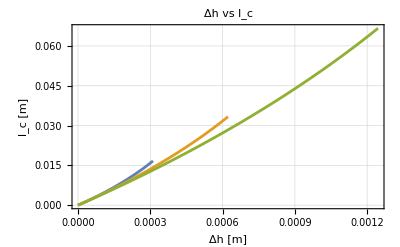
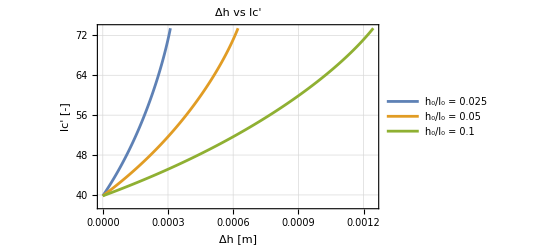

```mathematica
Row[{
ListPlot[Table[CombineVec[Delta@geomresc[[i,1]],geomresc[[i,2]]],{i,1,3}],Joined->True,Evaluate@opts,PlotRange->All,FrameLabel->{"Δh [m]","l_c [m]"},PlotLabel->"Δh vs l_c"],
ListPlot[Table[CombineVec[Delta@geomresc[[i,1]],NumDer[Delta@geomresc[[i,1]],geomresc[[i,2]]]],{i,1,3}],Joined->True,Evaluate@opts,PlotRange->All,FrameLabel->{"Δh [m]","lc' [-]"},PlotLabel->"Δh vs lc'",PlotLegends->AddLegend[Table[StringJoin["h_0/l_0 = ",ToString[arsamel0[[i]]]],{i,1,Length@geoms}],Right,Bottom]]
}]
```

### Force

#### Varying aspect ratio

```mathematica
Fsmallerh0[V_]:=F[h,V]/.celldata/.lc'[h]->NumDer[smallerh0[[1]],smallerh0[[2]]];
Fbiggerh0[V_]:=F[h,V]/.celldata/.lc'[h]->NumDer[biggerh0[[1]],biggerh0[[2]]];
```

```mathematica
forcesVmax={Fsmallerh0[Last@Vrange],Fnom[Last@Vrange],Fbiggerh0[Last@Vrange]};
```

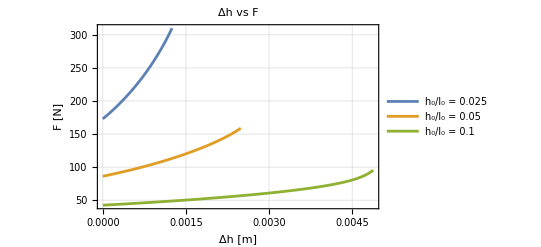

```mathematica
Show[
ListPlot[
Table[CombineVec[Delta[4geoms[[i,1]]],forcesVmax[[i]]],{i,1,Length@geoms}],Joined->True,
PlotLegends->AddLegend[Table["h_0/l_0 = "<>ToString[arsamel0[[i]]],{i,1,Length@geoms}],Right,Bottom],Evaluate@opts],
Evaluate@opts,PlotRange->All,FrameLabel->{"Δh [m]","F [N]"},PlotLabel->"Δh vs F",AxesOrigin->{0,0}
]
```

#### Rescaling

```mathematica
Fsmallersamear[V_]:=F[h,V]/.celldata/.lc'[h]->NumDer[smallersamear[[1]],smallersamear[[2]]];
Fbiggersamear[V_]:=F[h,V]/.celldata/.lc'[h]->NumDer[biggersamear[[1]],biggersamear[[2]]];
```

```mathematica
forcesrescVmax={Fsmallersamear[Last@Vrange],Fnom[Last@Vrange],Fbiggersamear[Last@Vrange]};
```

```mathematica
Table["h_0 = "<>ToString[h0rangetest[[i]]]<>" l_0 = "<>ToString[l0rangetest[[i]]],{i,1,Length@geoms}]
```

{h_0 = 0.00125 l_0 = 0.025,h_0 = 0.0025 l_0 = 0.05,h_0 = 0.005 l_0 = 0.1}

```mathematica
l0rangetest
```

{0.025,0.05,0.1}

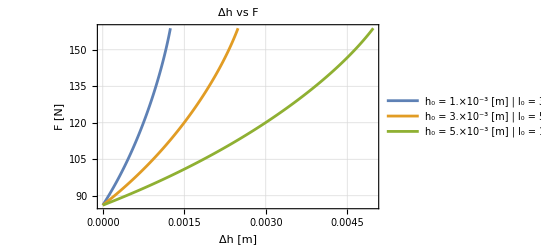

```mathematica
Show[
ListPlot[
Table[CombineVec[Delta[4geomresc[[i,1]]],forcesrescVmax[[i]]],{i,1,Length@geoms}],Joined->True,
PlotLegends->AddLegend[Table["h_0 = "<>ScientString[h0rangetest[[i]],1]<>" [m] | l_0 = "<>ScientString[l0rangetest[[i]],1]<>" [m]",{i,1,Length@geoms}],Right,Bottom],Evaluate@opts],
Evaluate@opts,PlotRange->All,FrameLabel->{"Δh [m]","F [N]"},PlotLabel->"Δh vs F",AxesOrigin->{0,0}
]
```

### Volume

```mathematica
Volfgeoms=Volf/.celldata/.{h->{smallerh0[[1]],nominalh0[[1]],biggerh0[[1]]},lc->{smallerh0[[2]],nominalh0[[2]],biggerh0[[2]]},R->{smallerh0[[3]],nominalh0[[3]],biggerh0[[3]]},θ->{smallerh0[[4]],nominalh0[[4]],biggerh0[[4]]},R0->{smallerh0[[3,1]],nominalh0[[3,1]],biggerh0[[3,1]]},θ0->{smallerh0[[4,1]],nominalh0[[4,1]],biggerh0[[4,1]]}};
```

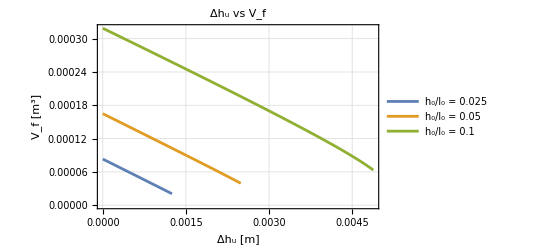

```mathematica
ListPlot[Table[CombineVec[Delta[4geoms[[i,1]]],Volfgeoms[[i]]],{i,1,Length@geoms}],
Joined->True,Evaluate@opts,FrameLabel->{"Δh_u [m]","V_f [m^3]"},PlotLabel->"Δh_u vs V_f",PlotLegends->AddLegend[Table[StringJoin["h_0/l_0 = ",ToString[arsamel0[[i]]]],{i,1,Length@geoms}],Right,Top]]
```

```mathematica
Volfresc=Volf/.celldata/.{h->{smallersamear[[1]],nominalh0[[1]],biggersamear[[1]]},lc->{smallersamear[[2]],nominalh0[[2]],biggersamear[[2]]},R->{smallersamear[[3]],nominalh0[[3]],biggersamear[[3]]},θ->{smallersamear[[4]],nominalh0[[4]],biggersamear[[4]]},R0->{smallersamear[[3,1]],nominalh0[[3,1]],biggersamear[[3,1]]},θ0->{smallersamear[[4,1]],nominalh0[[4,1]],biggersamear[[4,1]]}};
```

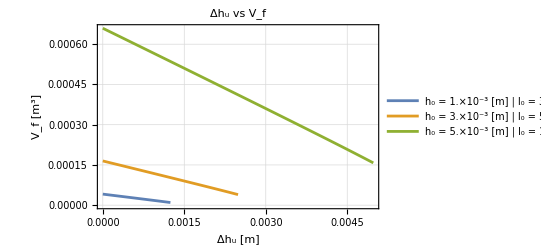

```mathematica
ListPlot[Table[CombineVec[Delta[4geomresc[[i,1]]],Volfresc[[i]]],{i,1,Length@geoms}],
Joined->True,Evaluate@opts,FrameLabel->{"Δh_u [m]","V_f [m^3]"},PlotLabel->"Δh_u vs V_f",PlotLegends->AddLegend[Table["h_0 = "<>ScientString[h0rangetest[[i]],1]<>" [m] | l_0 = "<>ScientString[l0rangetest[[i]],1]<>" [m]",{i,1,Length@geoms}],Right,Top]]
```

#### Energy

```mathematica
Uelgeoms=Table[CumTrapz[4geoms[[i,1]],forcesVmax[[i]]],{i,1,3}];
```

```mathematica
Uelresc=Table[CumTrapz[4geomresc[[i,1]],forcesrescVmax[[i]]],{i,1,3}];
```

```mathematica
uelgeoms=Uelgeoms/Volfgeoms[[;;,1]];
```

```mathematica
uelresc=Uelresc/Volfresc[[;;,1]];
```

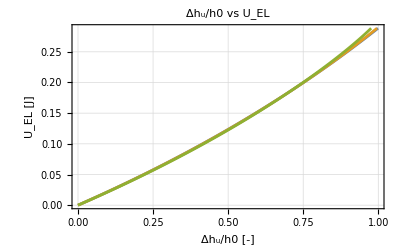
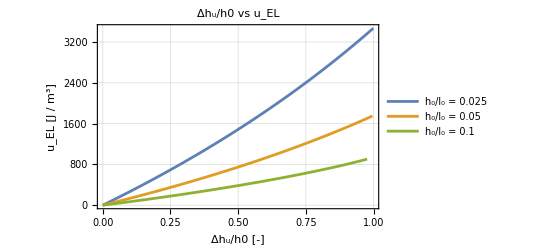

```mathematica
Row[{
ListPlot[Table[CombineVec[Delta[4geoms[[i,1]]]/geoms[[i,1,1]],Uelgeoms[[i]]],{i,1,Length@forcesVmax}],Joined->True,Evaluate@opts,FrameLabel->{"Δh_u/h0 [-]","U_EL [J]"},PlotLabel->"Δh_u/h0 vs U_EL"],Spacer@10,
ListPlot[Table[CombineVec[Delta[4geoms[[i,1]]]/geoms[[i,1,1]],uelgeoms[[i]]],{i,1,Length@forcesVmax}],Joined->True,Evaluate@opts,FrameLabel->{"Δh_u/h0 [-]","u_EL [J / m^3]"},PlotLabel->"Δh_u/h0 vs u_EL",PlotLegends->AddLegend[Table[StringJoin["h_0/l_0 = ",ToString[aspratios[[i,2]]]],{i,1,Length@geoms}],Left,Top]]}]
```

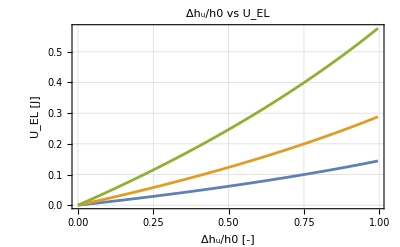
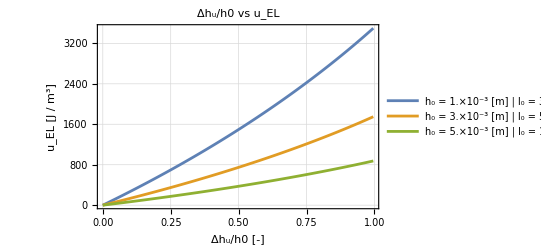

```mathematica
Row[{
ListPlot[Table[CombineVec[Delta[4geomresc[[i,1]]]/geomresc[[i,1,1]],Uelresc[[i]]],{i,1,Length@forcesrescVmax}],Joined->True,Evaluate@opts,FrameLabel->{"Δh_u/h0 [-]","U_EL [J]"},PlotLabel->"Δh_u/h0 vs U_EL"],Spacer@10,
ListPlot[Table[CombineVec[Delta[4geomresc[[i,1]]]/geomresc[[i,1,1]],uelresc[[i]]],{i,1,Length@forcesrescVmax}],Joined->True,Evaluate@opts,FrameLabel->{"Δh_u/h0 [-]","u_EL [J / m^3]"},PlotLabel->"Δh_u/h0 vs u_EL",PlotLegends->AddLegend[Table["h_0 = "<>ScientString[h0rangetest[[i]],1]<>" [m] | l_0 = "<>ScientString[l0rangetest[[i]],1]<>" [m]",{i,1,Length@geoms}],Left,Top]]}]
```

### Energy as a function of l0

```mathematica
l0vec=l0 Range[0.5,2,0.05]/.data0nominal;
```

```mathematica
h0vec=aspratios[[2,2]] l0vec;
```

```mathematica
aspratios//MatrixForm
```

(0.05 | 0.025 | 0.0125
0.1 | 0.05 | 0.025
0.2 | 0.1 | 0.05)

```mathematica
geomsh0l0vec=Table[solvegeom[h0vec[[i]],l0vec[[i]],500],{i,1,Length@l0vec}];
```

```mathematica
forcesVmaxvecs=F[h,Last@Vrange]/.celldata/.lc'[h]->Table[NumDer[geomsh0l0vec[[i,1]],geomsh0l0vec[[i,2]]],{i,1,Length@l0vec}];
```

```mathematica
Uelvec=Table[Trapz[4geomsh0l0vec[[i,1]],forcesVmaxvecs[[i]]],{i,1,Length@l0vec}]//Flatten;
```

```mathematica
Volmaxvec=(Volf/.celldata/.{h->geomsh0l0vec[[;;,1]],lc->geomsh0l0vec[[;;,2]],R->geomsh0l0vec[[;;,3]],θ->geomsh0l0vec[[;;,4]],R0->geomsh0l0vec[[;;,3,1]],θ0->geomsh0l0vec[[;;,4,1]]})[[;;,1]];
```

```mathematica
uelvec=Uelvec/Volmaxvec;
```

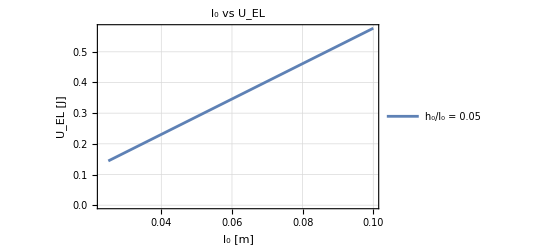
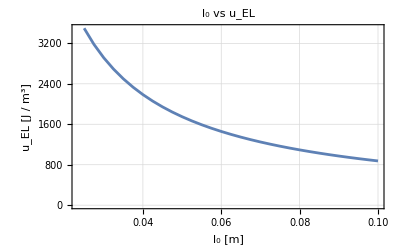

```mathematica
Row[{
ListPlot[CombineVec[l0vec,Uelvec],Joined->True,Evaluate@opts,FrameLabel->{"l_0 [m]","U_EL [J]"},PlotLabel->"l_0 vs U_EL",PlotLegends->AddLegend[{"h_0/l_0 = "<>ToString@aspratios[[2,2]]}]],
ListPlot[CombineVec[l0vec,uelvec],Joined->True,Evaluate@opts,FrameLabel->{"l_0 [m]","u_EL [J / m^3]"},PlotLabel->"l_0 vs u_EL"]

}]
```

### Find proper geometries

```mathematica
tp0vec=0.167 10^-3//N
```

0.000167

```mathematica
Vmaxvec=50 10^3
```

50000

```mathematica
Clear@geomtest
```

```mathematica
{l0test=20 10^-2,h0test=0.05l0test}
geomtest=solvegeom[h0test,l0test,1000];
```

{1/5,0.01}

```mathematica
Uelmax=(1/2 CC Vmaxvec^2/.tp0->tp0vec/.celldata/.lc[h]->Max@geomtest[[2]])
```

14.4694

```mathematica
Nu=100000/(Uelmax 0.1)//Ceiling
```

69112

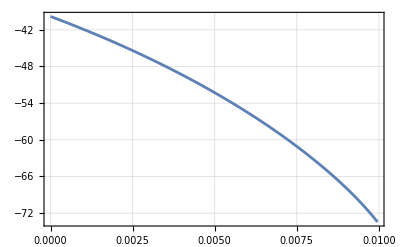

```mathematica
ListPlot[CombineVec[Delta[4geomtest[[1]]],NumDer[geomtest[[1]],geomtest[[2]]]],Joined->True,Evaluate@opts]
```

```mathematica
CC /.tp0->tp0vec/.celldata/.lc[h]->Max@geomtest[[2]]
```

1.15756×10^-8

```mathematica
F[h,V]
```

-(V^2 w0 ϵf ϵp lc'[h])/(8 (2 tp0 ϵf+tf0 ϵp))

```mathematica
F[h,V]/.tp0->tp0vec/.celldata/.lc'[h]->NumDer[geomtest[[1]],geomtest[[1]]]/.V->Vmaxvec;
```

```mathematica
Ftest=F[h,V]/.tp0->tp0vec/.celldata/.lc'[h]->NumDer[geomtest[[1]],geomtest[[2]]]/.V->Vmaxvec;
```

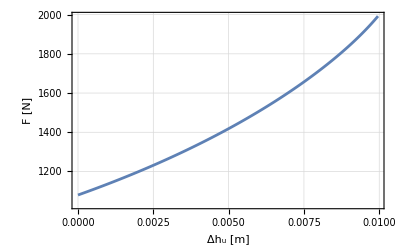

```mathematica
ListPlot[CombineVec[Delta[4geomtest[[1]]],Ftest],
Joined->True,Evaluate@opts,FrameLabel->{"Δh_u [m]","F [N]"},PlotLegends->AddLegend["V = "<>ToString[#]<>" [V]"&/@Vmaxvec]]
```

```mathematica
Trapz[4geomtest[[1]],Ftest]
```

{14.4694}

### Compare with 1DOF and 2DOF

```mathematica
l0rangetest[[2]]
```

0.05

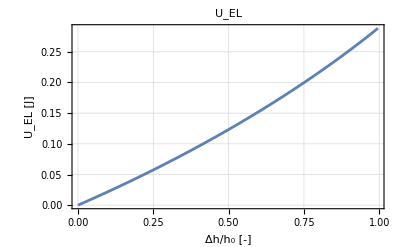
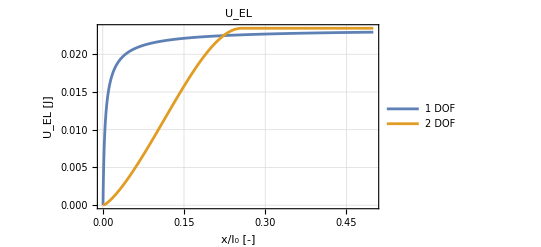

```mathematica
Row[{
ListPlot[CombineVec[Delta[4geomresc[[2,1]]]/geomresc[[2,1,1]],Uelresc[[2]]],Joined->True,PlotRange->All,Evaluate@opts,FrameLabel->{"Δh/h_0 [-]","U_EL [J]"},PlotLabel->"U_EL"],Spacer@10,
ListPlot[{CombineVec[(oneDOF["PSTRAIN","xrange"][[2]])/(oneDOF["l0range"][[2]]),oneDOF["PSTRAIN","Uelx"]],CombineVec[twoDOF["PSTRAIN","xrange"]/(twoDOF["l0range"][[2]]),twoDOF["PSTRAIN","Uelx"]]}
,Joined->True,PlotRange->All,Evaluate@opts,FrameLabel->{"x/l_0 [-]","U_EL [J]"},PlotLabel->"U_EL",PlotLegends->AddLegend[{"1 DOF","2 DOF"},Right,Center]]}
]
```

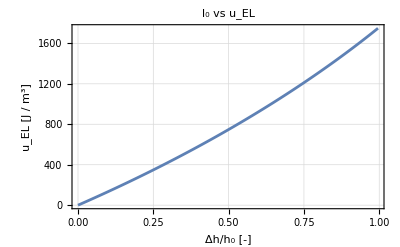
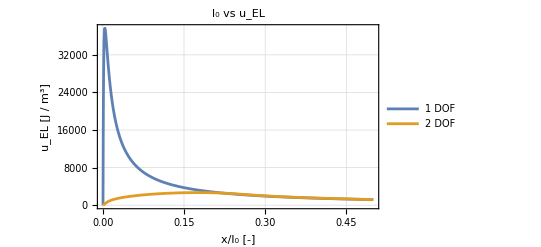

```mathematica
Row[{
ListPlot[CombineVec[Delta[4geomresc[[2,1]]]/geomresc[[2,1,1]],uelresc[[2]]],Joined->True,PlotRange->All,Evaluate@opts,FrameLabel->{"Δh/h_0 [-]","u_EL [J / m^3]"},PlotLabel->"l_0 vs u_EL"],Spacer@10,
ListPlot[{CombineVec[(oneDOF["PSTRAIN","xrange"][[2]])/(oneDOF["l0range"][[2]]),oneDOF["PSTRAIN","uelx"]],CombineVec[twoDOF["PSTRAIN","xrange"]/(twoDOF["l0range"][[2]]),twoDOF["PSTRAIN","uelx"]]}
,Joined->True,PlotRange->All,Evaluate@opts,FrameLabel->{"x/l_0 [-]","u_EL [J / m^3]"},PlotLabel->"l_0 vs u_EL",PlotLegends->AddLegend[{"1 DOF","2 DOF"},Right]]}
]
```

### Q-V plot

C = Q / V

```mathematica
{Cmin=Min@Cnom,Cmax=Max@Cnom}
```

{0.,1.60243×10^-8}

```mathematica
Vmaxdef=LinSpace[0,Last@Vrange,Length@Cnom];
```

```mathematica
Qmaxdef=Cmax Vmaxdef;
```

```mathematica
Vmindef=LinSpace[0,Last@Vrange,Length@Cnom];
```

```mathematica
Qmindef=Cmin Vmindef;
```

```mathematica
QVmax=LinSpace[0,Last@Qmaxdef,Length@Cnom];
```

```mathematica
Vmaxvec=ConstantArray[Last@Vrange,Length@Cnom];
```

```mathematica
QVpl[style_:Automatic]:=ListPlot[{
CombineVec[Qmindef,Vmindef],CombineVec[Qmaxdef,Vmaxdef],CombineVec[QVmax,Vmaxvec]},PlotStyle->style,
Joined->True,FrameLabel->{"Q [A]","V [V]"},PlotLabel->"Q vs V",Evaluate@opts,PlotLegends->AddLegend[{"Min. def.","Max. def.","V_MAX"},Right,Bottom]]
```

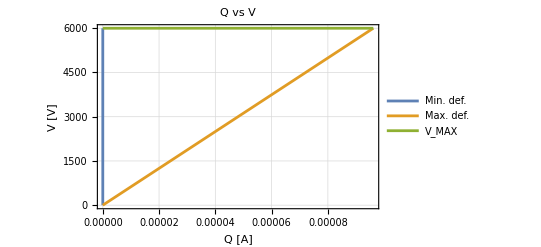

```mathematica
QVpl[]
```

```mathematica
UelQV=CumTrapz[QVmax,Vmaxvec]-CumTrapz[Qmaxdef,Vmaxdef];
```

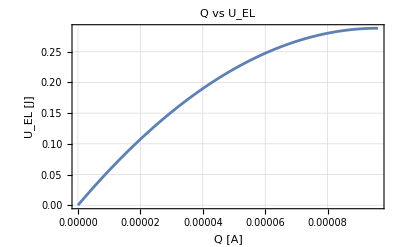

```mathematica
ListPlot[CombineVec[QVmax,UelQV],Joined->True,FrameLabel->{"Q [A]","U_EL [J]"},PlotLabel->"Q vs U_EL",Evaluate@opts]
```

#### Q-V plots in working condition

```mathematica
Cint=Interpolation[CombineVec[Delta@hunom,Cnom]];
FintV0=Interpolation[CombineVec[Delta@hunom,Fnom@0]];
FintVmax=Interpolation[CombineVec[Delta@hunom,Fnom[Last@Vrange]]];
```

```mathematica
fixedhpath[n_,Δhleft_,Δhright_,FintV0_,FintVmax_,Cint_,Vrange_]:=Module[{ΔhA,ΔhB,ΔhC,ΔhD,ΔhrangeAB,ΔhrangeBC,ΔhrangeCD,ΔhrangeDA,VAB,VBC,VCD,VDA,CAB,CBC,CCD,CDA,QAB,QBC,QCD,QDA},
ΔhA=Δhright;
ΔhB=Δhleft;
ΔhC=ΔhB;
ΔhD=ΔhA;
ΔhrangeAB=LinSpace[ΔhA,ΔhB,n];ΔhrangeBC=ConstantArray[ΔhB,n];ΔhrangeCD=LinSpace[ΔhC,ΔhD,n];ΔhrangeDA=ConstantArray[ΔhA,n];
VAB=ConstantArray[Vrange[[1]],n];VBC=LinSpace[Vrange[[1]],Last@Vrange,n];VCD=ConstantArray[Last@Vrange,n];VDA=LinSpace[Last@Vrange,Vrange[[1]],n];
CAB=Cint[ ΔhrangeAB];CBC=Cint[ΔhrangeBC];CCD=Cint[ΔhrangeCD];CDA=Cint[ΔhrangeDA];
QAB=CAB VAB;QBC=CBC VBC;QCD=CCD VCD;QDA=CDA VDA;
{{{ΔhA,FintV0[ΔhA]},{ΔhB,FintV0[ΔhB]},{ΔhC,FintVmax[ΔhC]},{ΔhD,FintVmax[ΔhD]}},{ΔhrangeAB,ΔhrangeBC,ΔhrangeCD,ΔhrangeDA},{VAB,VBC,VCD,VDA},{CAB,CBC,CCD,CDA},{QAB,QBC,QCD,QDA}}]
```

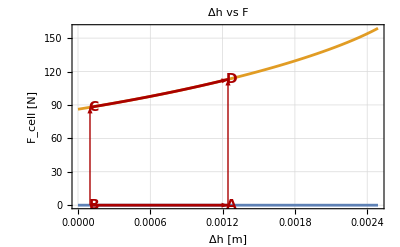
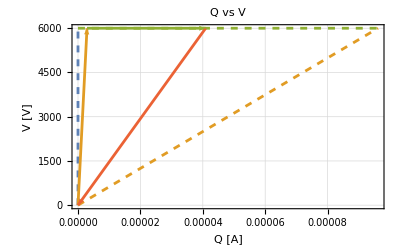

```mathematica
Module[{Δhleft=Nearest[Delta[hunom],0.0001][[1]],Δhright=0.5Last@Delta[hunom],xtol=0.00003,ytol=0.5,ptsdh,hrangesdh,Vrangesdh,Crangesdh,Qrangesdh},
{ptsdh,hrangesdh,Vrangesdh,Crangesdh,Qrangesdh}=fixedhpath[100,Δhleft,Δhright,FintV0,FintVmax,Cint,Vrange];
Row[{
Show[
Plot[{FintV0[dh],FintVmax[dh]},{dh,Delta[hunom][[1]],Last@Delta[hunom]},Evaluate@opts,FrameLabel->{"Δh [m]","F_cell [N]"},PlotLabel->"Δh vs F"],
Plot[{FintV0[dh]},{dh,Δhleft,Δhright},PlotStyle->{Darker@Red,Thick}] /.MidArrow[-1],
Plot[{FintVmax[dh]},{dh,Δhleft,Δhright},PlotStyle->Darker@Red] /.MidArrow[1],
Graphics[{Thick,Darker@Red,
Line[{{Δhleft,FintV0@Δhleft},{Δhleft,FintVmax@Δhleft}}]/.MidArrow[1],
Line[{{Δhright,FintV0@Δhright},{Δhright,FintVmax@Δhright}}]/.MidArrow[-1],
MapThread[Text[Style[#1,{Bold,14}],#2+{xtol,ytol}]&,{{"A","B","D","C"},Flatten[Table[{j,i[j]},{i,{FintV0,FintVmax}},{j,{Δhright,Δhleft}}],1]}]}]
],
Show[
QVpl[Dashed],
ListPlot[Table[Transpose[{Qrangesdh[[i]],Vrangesdh[[i]]}],{i,1,Length@Qrangesdh}],Joined->True,PlotLegends->AddLegend[{"AB (Origin)","BC","CD","DA"},Right,Bottom],Evaluate@opts]/.MidArrow[1]]}]

]
```

### Stack

```mathematica
Manipulate[
Block[{tf0=tf0/.celldata,hlcRθ=geoms[[2,;;,idx]],hlcRθ0=If[undef==1,geoms[[2,;;,1]],{}]},
Show[
Table[Table[DrawCell[hlcRθ,hlcRθ0,{(j-Floor@(Ncol/2)) 1.1l0/.data0nominal,(i-1)2hlcRθ[[1]]+tf0}],{i,1,Ncells}],{j,0,Ncol-1}],
PlotRange->Max[Ncol,Ncells](l0/.data0nominal){{-0.9,0.9},{-0.05,0.2}},(*PlotRange->{Max[Ncol,Ncells](l0/.data0nominal){-1,1},Max[Ncol,Ncells](h0/.data0nominal){-1,2}},*)Evaluate@opts,Axes->True,FrameLabel->{"x [m]","y [m]"},ImageSize->1000]]
,Row[{
Control[{idx,1,Length@geoms[[1,1]],1}],Spacer@10,
Control[{{Ncol,1,"Columns"},1,5,1}],Spacer@10,
Control[{{Ncells,2,"Cells"},2,5,1}],Spacer@10,
Control[{{undef,1,"Undeformed"},{0,1}}]}]]
```

#### Force

Cs = (Ncells-1)C,
hs = Ncells/2 4h =2 Ncells h
dCs/dhs=(Ncells-1)/(2 Ncells)dC/dh

```mathematica
Fs[V_,Ncells_]:=-V^2/2(Ncells-1)/(2 Ncells)D[CC,h]/.D[lc[h],h]->NumDer[hnom,lcnom]/.celldata
```

```mathematica
Hs[Ncells_]:=Ncells/2 hunom
```

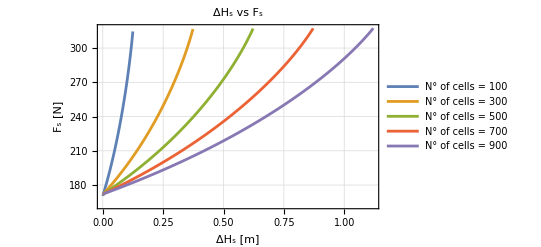

```mathematica
ListPlot[Table[CombineVec[Delta@Hs[Ncells],Fs[Last@Vrange,Ncells]],{Ncells,100,1000,200}],Joined->True,FrameLabel->{"ΔH_s [m]","F_s [N]"},PlotLabel->"ΔH_s vs F_s",PlotLegends->AddLegend[Table[StringJoin["N° of cells = ",ToString[Ncells]],{Ncells,100,1000,200}],Right,Bottom],Evaluate@opts]
```

```mathematica
UelNcells=Table[Trapz[Delta@Hs[Ncells],Fs[Last@Vrange,Ncells]],{Ncells,2,100,1}]//Flatten;
```

```mathematica
uelNcells=UelNcells/Table[(Ncells-1)Volfgeoms[[2,1]],{Ncells,2,100,1}];
```

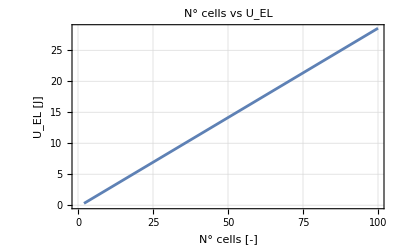
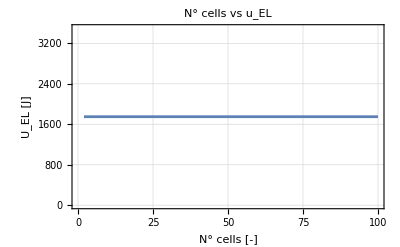

```mathematica
Row[{
ListPlot[CombineVec[Range[2,100],UelNcells],Joined->True,FrameLabel->{"N° cells [-]","U_EL [J]"},PlotLabel->"N° cells  vs U_EL ",Evaluate@opts],
ListPlot[CombineVec[Range[2,100],uelNcells],Joined->True,FrameLabel->{"N° cells [-]","U_EL [J]"},PlotLabel->"N° cells  vs u_EL ",Evaluate@opts]}]
```

### Save

```mathematica
toexp=Association[
"data0"->data0nominal,"nomgeom"->geomtest[[1]],"C"->CC,"F"->F[h,V],"Uelmax"->Uelmax];
Export["lenscell.m",toexp]
```

lenscell.m